```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
SetDirectory[NotebookDirectory[]];
Needs["gUtils`"];
Needs["gBRDF`"];
Needs["sgCommon`"];
Needs["gPlots`"];
Needs["gPlots3D`"];
Needs["gSphericalCap`"];
```

```mathematica
Csc[1/2 (θL+ArcCot[Cos[θ1]/(k+ Sin[θ1])])] Sin[(θ1+θL)/2]//FullSimplify
```

Csc[1/2 (θL+ArcTan[Sec[θ1] (k+Sin[θ1])])] Sin[(θ1+θL)/2]

```mathematica
Series[Csc[1/2 (θL+ArcTan[Sec[θ1] (k+Sin[θ1])])] Sin[(θ1+θL)/2],{k,0,1}]//FullSimplify
```

Csc[1/2 (θL+ArcTan[Tan[θ1]])] Sin[(θ1+θL)/2]-1/2 (Cos[θ1] Cot[1/2 (θL+ArcTan[Tan[θ1]])] Csc[1/2 (θL+ArcTan[Tan[θ1]])] Sin[(θ1+θL)/2]) k+O[k]^2

```mathematica
jaco=(θ1+θL)/(θL+ArcCot[Cos[θ1]/(k+ Sin[θ1])]);
sinDiv=Csc[1/2 (θL+ArcCot[Cos[θ1]/(k+ Sin[θ1])])] Sin[(θ1+θL)/2];
afunc1=jaco*sinDiv;
elem1=Cos[θ1];
elem2=Cos[θL];
elem3=Cos[θ1+θL];
bfunc1=(a1+k*(b1*elem1+c1*elem2));
bfunc2=(a2+(b2*elem1+c2*elem2));
bfunc3=k1+(k2+k3*elem3+k4*elem3*k+k5*k+k6*elem3^2);
Quiet@FindMinimum[NIntegrate[Abs[afunc1-(bfunc3/(bfunc1*bfunc2))],{θ1,0,π/2},{θL,0,π/2},{k,0,1},
PrecisionGoal->1,AccuracyGoal->1, Method->"QuasiMonteCarlo",MaxRecursion->2],
{a1,1},{b1,1},{c1,1},
{d1,1},{e1,1},{f1,1},{g1,1},
{a2,1},{b2,1},{c2,1},
{d2,1},{e2,1},{f2,1},{g2,1},
{a3,1},{b3,1},{c3,1},
{k1,1},{k2,1},{k3,1},{k4,1},{k5,1},{k6,1},{k7,1},{k8,1},{k9,1},{k10,1},{k11,1},{k12,1},{k13,1},
  {k14,1},{k15,1},{k16,1},{k17,1},{k18,1},{k19,1},{k20,1},
{k21,1},{k22,1},{k23,1},{k24,1},{k25,1},{k26,1},{k27,1},{k28,1},{k29,1}]
```

{0.0885322,{a1→3.18821,b1→2.13308,c1→0.585428,d1→1.,e1→1.,f1→1.,g1→1.,a2→4.02894,b2→-0.439104,c2→-0.874512,d2→1.,e2→1.,f2→1.,g2→1.,a3→1.,b3→1.,c3→1.,k1→5.11586,k2→5.11586,k3→-2.52595,k4→-3.36299,k5→-0.270021,k6→-2.03277,k7→1.,k8→1.,k9→1.,k10→1.,k11→1.,k12→1.,k13→1.,k14→1.,k15→1.,k16→1.,k17→1.,k18→1.,k19→1.,k20→1.,k21→1.,k22→1.,k23→1.,k24→1.,k25→1.,k26→1.,k27→1.,k28→1.,k29→1.}}

```mathematica
Csc[1/2 (θL+ArcCot[Cos[θ1]/(k+ Sin[θ1])])] Sin[(θ1+θL)/2]//FullSimplify

Plot[Sin[x]/Sin[2x],{x,0,π/2}];
```

Csc[1/2 (θL+ArcTan[Sec[θ1] (k+Sin[θ1])])] Sin[(θ1+θL)/2]

```mathematica
Csc[1/2 (θL+ArcTan[Sec[θ1] (k+Sin[θ1])])] Sin[(θ1+θL)/2];
Series[ArcTan[Sec[θ1] (k+Sin[θ1])],{k,0,1}]
```

ArcTan[Tan[θ1]]+(Sec[θ1] k)/(1+Tan[θ1]^2)+O[k]^2

```mathematica
Csc[1/2 (θL+θ1+(Sec[θ1] k)/(1+Tan[θ1]^2))] Sin[(θ1+θL)/2];
```

```mathematica
Series[Csc[1/2 (θL+ArcTan[Sec[θ1] (k+Sin[θ1])])] ,{k,0,1}]
```

Csc[1/2 (θL+ArcTan[Tan[θ1]])]-((Cot[1/2 (θL+ArcTan[Tan[θ1]])] Csc[1/2 (θL+ArcTan[Tan[θ1]])] Sec[θ1]) k)/(2 (1+Tan[θ1]^2))+O[k]^2

```mathematica
((Cot[1/2 (θL+θ1)] Csc[1/2 (θL+θ1)] Sec[θ1]) k)/(2 (1+Tan[θ1]^2))Sin[(θ1+θL)/2]//FullSimplify
```

1/2 k Cos[θ1] Cot[(θ1+θL)/2]

```mathematica
Series[(θ1+θL)/(θL+ArcCot[Cos[θ1]/(k+ Sin[θ1])]),{k,0,1}]
((θ1+θL) Sec[θ1] k)/((θL+θ1)^2 (1+Tan[θ1]^2))//FullSimplify
```

(θ1+θL)/(θL+ArcTan[Tan[θ1]])-((θ1+θL) Sec[θ1] k)/((θL+ArcTan[Tan[θ1]])^2 (1+Tan[θ1]^2))+O[k]^2

(k Cos[θ1])/(θ1+θL)

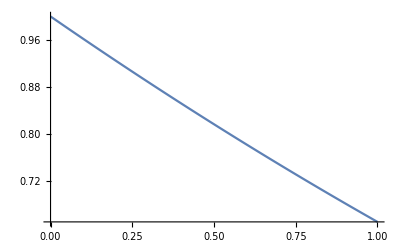

```mathematica
jacoSim1=1-(k Cos[θ1])/(θ1+θL);
divSim1=1-1/2 k Cos[θ1] Cot[(θ1+θL)/2];
jacoSim=Max[jacoSim1,0];
divSim=Max[divSim1,0];

Plot[(jacoSim*divSim)/.{θ1->π/3,θL->π/3},{k,0,1}]
```

```mathematica
sgPolar[θ,λ,μ]/sgPolar[0,λ,μ]
```

ⅇ^(λ (-1+Cos[θ]))